```mathematica
SetDirectory[NotebookDirectory[]]
```

SetDirectory[$Failed]

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

SetDirectory::badfile: The specified argument, $Failed, should be a valid string or File object.

```mathematica
Get["library/FeynCalc.m"]
```

TagSetDelayed::write: Tag Commutator in Commutator[a_, b_] = c_ is Protected.

SetDelayed::write: Tag Commutator in MakeBoxes[Commutator[a_, b_], TraditionalForm] is Protected.

Set::write: Tag Commutator in Commutator[RightPartialD[x_], LeftPartialD[y_]] is Protected.

TagSetDelayed::write: Tag Commutator in Commutator[a_, b_] = c_ is Protected.

SetDelayed::write: Tag Commutator in MakeBoxes[Commutator[a_, b_], TraditionalForm] is Protected.

## Explicit Gell-Mann matrices

```mathematica
Λ={{{0,0,0},{0,0,1/(2 √3)},{0,1/(2 √3),0}},{{0,0,1/(2 √3)},{0,0,0},{1/(2 √3),0,0}},{{0,1/(2 √3),0},{1/(2 √3),0,0},{0,0,0}},{{1/(2 √3),0,0},{0,-1/(2 √3),0},{0,0,0}},{{-1/6,0,0},{0,-1/6,0},{0,0,1/3}}};
```

```mathematica
dband[k_]:=3{k.Λ[[1]].k,k.Λ[[2]].k,k.Λ[[3]].k,k.Λ[[4]].k,k.Λ[[5]].k}
```

## Spin 3/2 matrices

```mathematica
Sz=1/2{{3,0,0,0},{0,1,0,0},{0,0,-1,0},{0,0,0,-3}};
Sx=1/2{{0,√3,0,0},{√3,0,2,0},{0,2,0,√3},{0,0,√3,0}};
Sy=1/2{{0,-I √3,0,0},{I √3,0,-I 2,0},{0,I 2,0,-I √3},{0,0,I √3,0}};
```

```mathematica
I4={{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}};
```

```mathematica
Sz//MatrixForm
```

(3/2 | 0 | 0 | 0
0 | 1/2 | 0 | 0
0 | 0 | -1/2 | 0
0 | 0 | 0 | -3/2)

```mathematica
Sx//MatrixForm
```

(0 | (√3)/2 | 0 | 0
(√3)/2 | 0 | 1 | 0
0 | 1 | 0 | (√3)/2
0 | 0 | (√3)/2 | 0)

```mathematica
Sy//MatrixForm
```

(0 | -(ⅈ √3)/2 | 0 | 0
(ⅈ √3)/2 | 0 | -ⅈ | 0
0 | ⅈ | 0 | -(ⅈ √3)/2
0 | 0 | (ⅈ √3)/2 | 0)

```mathematica
LHam[k,B]:=Eigenvalues[]
```

```mathematica
Plot3D[{0,EigS[{ky,kz,0},{0,0,0.25},1]},{ky,-2,2},{kz,-2,2},PlotRange->{-2,2},ClippingStyle->None,BoxRatios->{1, 1, 1},PlotStyle->{{RGBColor[255/255,194/255,10/255],Opacity[0.25]},{RGBColor[12/255,123/255,220/255],Opacity[0.75]}},Mesh->None,ViewPoint->{1.2, -2.4, 1.8},ImageSize->500,Axes->False,Boxed->False,Lighting->{"Ambient",White,{1.2, -2.4, 1.2}}]
```

-Graphics3D-

```mathematica
Sx.Sz+Sz.Sx//MatrixForm
```

(0 | √3 | 0 | 0
√3 | 0 | 0 | 0
0 | 0 | 0 | -√3
0 | 0 | -√3 | 0)

```mathematica
idM={{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}};
```

```mathematica
Comm[X_,Y_]:=X.Y-Y.X
```

```mathematica
AntiComm[X_,Y_]:=X.Y+Y.X
```

```mathematica
Sz.Sz-5/4 idM
```

{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,1}}

## Gamma matrices

```mathematica
Γ={1/(√3)(Sy.Sz+Sz.Sy),1/(√3)(Sz.Sx+Sx.Sz),1/(√3)(Sx.Sy+Sy.Sx),1/(√3)(Sx.Sx-Sy.Sy),Sz.Sz-5/4 idM};
```

```mathematica
Γ[[5]]
```

{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,1}}

```mathematica
ix=1;
Γ[[ix]]//MatrixForm
Γ[[ix]]ᵀ//MatrixForm
```

(0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0)

(0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0)

```mathematica
ix=2;
Γ[[ix]]//MatrixForm
Γ[[ix]]ᵀ//MatrixForm
```

(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0)

(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0)

```mathematica
ix=3;
Γ[[ix]]//MatrixForm
Γ[[ix]]ᵀ//MatrixForm
```

(0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ
ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0)

(0 | 0 | ⅈ | 0
0 | 0 | 0 | ⅈ
-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0)

```mathematica
ix=4;
Γ[[ix]]//MatrixForm
Γ[[ix]]ᵀ//MatrixForm
```

(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0)

(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0)

```mathematica
Γ[[1]].Γ[[1]]
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
Γ[[3]]ᵀ.Γ[[1]]ᵀ.Γ[[1]].Γ[[3]]
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
ix=5;
Γ[[ix]]//MatrixForm
Γ[[ix]]ᵀ//MatrixForm
```

(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1)

(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1)

```mathematica
Γ[[2]]//MatrixForm
```

(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0)

```mathematica
Γ[[3]]//MatrixForm
```

(0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ
ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0)

```mathematica
Γ[[4]]//MatrixForm
```

(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0)

```mathematica
Γ[[3]]ᵀ-Γ[[3]]*
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
A={{0,0,0,1/4,(√3)/4},{0,0,1/4,0,0},{0,-1/4,0,0,0},{-1/4,0,0,0,0},{(-√3)/4,0,0,0,0}}
```

{{0,0,0,1/4,(√3)/4},{0,0,1/4,0,0},{0,-1/4,0,0,0},{-1/4,0,0,0,0},{-(√3)/4,0,0,0,0}}

```mathematica
A+Aᵀ
```

{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

```mathematica
B={{0,0,1/4,0,0},{0,0,0,1/4,(-√3)/4},{-1/4,0,0,0,0},{0,-1/4,0,0,0},{0,(√3)/4,0,0,0}}
```

{{0,0,1/4,0,0},{0,0,0,1/4,-(√3)/4},{-1/4,0,0,0,0},{0,-1/4,0,0,0},{0,(√3)/4,0,0,0}}

```mathematica
B+Bᵀ
```

{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

```mathematica
CC={{0,-1/4,0,0,0},{1/4,0,0,0,0},{0,0,0,-1/2,0},{0,0,1/2,0,0},{0,0,0,0,0}}
```

{{0,-1/4,0,0,0},{1/4,0,0,0,0},{0,0,0,-1/2,0},{0,0,1/2,0,0},{0,0,0,0,0}}

```mathematica
CC+CCᵀ
```

{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

```mathematica
η={A,B,CC}
```

{{{0,0,0,1/4,(√3)/4},{0,0,1/4,0,0},{0,-1/4,0,0,0},{-1/4,0,0,0,0},{-(√3)/4,0,0,0,0}},{{0,0,1/4,0,0},{0,0,0,1/4,-(√3)/4},{-1/4,0,0,0,0},{0,-1/4,0,0,0},{0,(√3)/4,0,0,0}},{{0,-1/4,0,0,0},{1/4,0,0,0,0},{0,0,0,-1/2,0},{0,0,1/2,0,0},{0,0,0,0,0}}}

```mathematica
Bx η[[1]]+By η[[2]]+Bz η[[3]]//MatrixForm
```

(0 | -Bz/4 | By/4 | Bx/4 | (√3 Bx)/4
Bz/4 | 0 | Bx/4 | By/4 | -(√3 By)/4
-By/4 | -Bx/4 | 0 | -Bz/2 | 0
-Bx/4 | -By/4 | Bz/2 | 0 | 0
-(√3 Bx)/4 | (√3 By)/4 | 0 | 0 | 0)

```mathematica
{Bx,By,Bz}.η//MatrixForm
```

(0 | -Bz/4 | By/4 | Bx/4 | (√3 Bx)/4
Bz/4 | 0 | Bx/4 | By/4 | -(√3 By)/4
-By/4 | -Bx/4 | 0 | -Bz/2 | 0
-Bx/4 | -By/4 | Bz/2 | 0 | 0
-(√3 Bx)/4 | (√3 By)/4 | 0 | 0 | 0)

```mathematica
SpinG[a_,b_]:=Comm[Γ[[a]],Γ[[b]]]/(2I)
```

```mathematica
SpinG[1,2].SpinG[1,2]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
SpinG[1,3].SpinG[1,3]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
SpinG[1,4].SpinG[1,4]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
SpinG[1,5].SpinG[1,5]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
SpinG[5,3].SpinG[5,3]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
DisP[k_,B_,g_]:=Module[{a,b,X,Y,Z,W},X=B.η;Y=Sum[SpinG[a,b]X[[a,b]],{a,1,5},{b,1,5}];Eigenvalues[Z=1/2(dband[k].Γ+2g Y)]]
```

```mathematica
DisP[{px,py,pz},{Hx,Hy,Hz},g]
```

{1/32 Root[589824 g^4 Hx^4-917504 g^4 Hx^2 Hy^2+589824 g^4 Hy^4-917504 g^4 Hx^2 Hz^2+1179648 g^4 Hy^2 Hz^2+589824 g^4 Hz^4-655360 g^2 Hx^2 px^4+131072 g^2 Hy^2 px^4+131072 g^2 Hz^2 px^4+65536 px^8+1572864 g^2 Hx Hy px^3 py-524288 g^2 Hx^2 px^2 py^2-524288 g^2 Hy^2 px^2 py^2+262144 g^2 Hz^2 px^2 py^2+262144 px^6 py^2-1572864 g^2 Hx Hy px py^3+131072 g^2 Hx^2 py^4-655360 g^2 Hy^2 py^4+131072 g^2 Hz^2 py^4+393216 px^4 py^4+262144 px^2 py^6+65536 py^8+1572864 g^2 Hx Hz px^3 pz-1572864 g^2 Hy Hz px^2 py pz-1572864 g^2 Hx Hz px py^2 pz-1572864 g^2 Hy Hz py^3 pz-524288 g^2 Hx^2 px^2 pz^2+262144 g^2 Hy^2 px^2 pz^2-524288 g^2 Hz^2 px^2 pz^2+262144 px^6 pz^2-1572864 g^2 Hx Hy px py pz^2+262144 g^2 Hx^2 py^2 pz^2-524288 g^2 Hy^2 py^2 pz^2-524288 g^2 Hz^2 py^2 pz^2+786432 px^4 py^2 pz^2+786432 px^2 py^4 pz^2+262144 py^6 pz^2-1572864 g^2 Hx Hz px pz^3-1572864 g^2 Hy Hz py pz^3+131072 g^2 Hx^2 pz^4+131072 g^2 Hy^2 pz^4-655360 g^2 Hz^2 pz^4+393216 px^4 pz^4+786432 px^2 py^2 pz^4+393216 py^4 pz^4+262144 px^2 pz^6+262144 py^2 pz^6+65536 pz^8+(65536 g^2 Hx^2 px^2+32768 g^2 Hy^2 px^2+32768 g^2 Hz^2 px^2-196608 g^2 Hx Hy px py-32768 g^2 Hx^2 py^2-65536 g^2 Hy^2 py^2+32768 g^2 Hz^2 py^2-196608 g^2 Hx Hz px pz-196608 g^2 Hy Hz py pz-32768 g^2 Hx^2 pz^2+32768 g^2 Hy^2 pz^2-65536 g^2 Hz^2 pz^2) #1+(-2560 g^2 Hx^2-2560 g^2 Hy^2-2560 g^2 Hz^2-512 px^4-1024 px^2 py^2-512 py^4-1024 px^2 pz^2-1024 py^2 pz^2-512 pz^4) #1^2+#1^4&,1],1/32 Root[589824 g^4 Hx^4-917504 g^4 Hx^2 Hy^2+589824 g^4 Hy^4-917504 g^4 Hx^2 Hz^2+1179648 g^4 Hy^2 Hz^2+589824 g^4 Hz^4-655360 g^2 Hx^2 px^4+131072 g^2 Hy^2 px^4+131072 g^2 Hz^2 px^4+65536 px^8+1572864 g^2 Hx Hy px^3 py-524288 g^2 Hx^2 px^2 py^2-524288 g^2 Hy^2 px^2 py^2+262144 g^2 Hz^2 px^2 py^2+262144 px^6 py^2-1572864 g^2 Hx Hy px py^3+131072 g^2 Hx^2 py^4-655360 g^2 Hy^2 py^4+131072 g^2 Hz^2 py^4+393216 px^4 py^4+262144 px^2 py^6+65536 py^8+1572864 g^2 Hx Hz px^3 pz-1572864 g^2 Hy Hz px^2 py pz-1572864 g^2 Hx Hz px py^2 pz-1572864 g^2 Hy Hz py^3 pz-524288 g^2 Hx^2 px^2 pz^2+262144 g^2 Hy^2 px^2 pz^2-524288 g^2 Hz^2 px^2 pz^2+262144 px^6 pz^2-1572864 g^2 Hx Hy px py pz^2+262144 g^2 Hx^2 py^2 pz^2-524288 g^2 Hy^2 py^2 pz^2-524288 g^2 Hz^2 py^2 pz^2+786432 px^4 py^2 pz^2+786432 px^2 py^4 pz^2+262144 py^6 pz^2-1572864 g^2 Hx Hz px pz^3-1572864 g^2 Hy Hz py pz^3+131072 g^2 Hx^2 pz^4+131072 g^2 Hy^2 pz^4-655360 g^2 Hz^2 pz^4+393216 px^4 pz^4+786432 px^2 py^2 pz^4+393216 py^4 pz^4+262144 px^2 pz^6+262144 py^2 pz^6+65536 pz^8+(65536 g^2 Hx^2 px^2+32768 g^2 Hy^2 px^2+32768 g^2 Hz^2 px^2-196608 g^2 Hx Hy px py-32768 g^2 Hx^2 py^2-65536 g^2 Hy^2 py^2+32768 g^2 Hz^2 py^2-196608 g^2 Hx Hz px pz-196608 g^2 Hy Hz py pz-32768 g^2 Hx^2 pz^2+32768 g^2 Hy^2 pz^2-65536 g^2 Hz^2 pz^2) #1+(-2560 g^2 Hx^2-2560 g^2 Hy^2-2560 g^2 Hz^2-512 px^4-1024 px^2 py^2-512 py^4-1024 px^2 pz^2-1024 py^2 pz^2-512 pz^4) #1^2+#1^4&,2],1/32 Root[589824 g^4 Hx^4-917504 g^4 Hx^2 Hy^2+589824 g^4 Hy^4-917504 g^4 Hx^2 Hz^2+1179648 g^4 Hy^2 Hz^2+589824 g^4 Hz^4-655360 g^2 Hx^2 px^4+131072 g^2 Hy^2 px^4+131072 g^2 Hz^2 px^4+65536 px^8+1572864 g^2 Hx Hy px^3 py-524288 g^2 Hx^2 px^2 py^2-524288 g^2 Hy^2 px^2 py^2+262144 g^2 Hz^2 px^2 py^2+262144 px^6 py^2-1572864 g^2 Hx Hy px py^3+131072 g^2 Hx^2 py^4-655360 g^2 Hy^2 py^4+131072 g^2 Hz^2 py^4+393216 px^4 py^4+262144 px^2 py^6+65536 py^8+1572864 g^2 Hx Hz px^3 pz-1572864 g^2 Hy Hz px^2 py pz-1572864 g^2 Hx Hz px py^2 pz-1572864 g^2 Hy Hz py^3 pz-524288 g^2 Hx^2 px^2 pz^2+262144 g^2 Hy^2 px^2 pz^2-524288 g^2 Hz^2 px^2 pz^2+262144 px^6 pz^2-1572864 g^2 Hx Hy px py pz^2+262144 g^2 Hx^2 py^2 pz^2-524288 g^2 Hy^2 py^2 pz^2-524288 g^2 Hz^2 py^2 pz^2+786432 px^4 py^2 pz^2+786432 px^2 py^4 pz^2+262144 py^6 pz^2-1572864 g^2 Hx Hz px pz^3-1572864 g^2 Hy Hz py pz^3+131072 g^2 Hx^2 pz^4+131072 g^2 Hy^2 pz^4-655360 g^2 Hz^2 pz^4+393216 px^4 pz^4+786432 px^2 py^2 pz^4+393216 py^4 pz^4+262144 px^2 pz^6+262144 py^2 pz^6+65536 pz^8+(65536 g^2 Hx^2 px^2+32768 g^2 Hy^2 px^2+32768 g^2 Hz^2 px^2-196608 g^2 Hx Hy px py-32768 g^2 Hx^2 py^2-65536 g^2 Hy^2 py^2+32768 g^2 Hz^2 py^2-196608 g^2 Hx Hz px pz-196608 g^2 Hy Hz py pz-32768 g^2 Hx^2 pz^2+32768 g^2 Hy^2 pz^2-65536 g^2 Hz^2 pz^2) #1+(-2560 g^2 Hx^2-2560 g^2 Hy^2-2560 g^2 Hz^2-512 px^4-1024 px^2 py^2-512 py^4-1024 px^2 pz^2-1024 py^2 pz^2-512 pz^4) #1^2+#1^4&,3],1/32 Root[589824 g^4 Hx^4-917504 g^4 Hx^2 Hy^2+589824 g^4 Hy^4-917504 g^4 Hx^2 Hz^2+1179648 g^4 Hy^2 Hz^2+589824 g^4 Hz^4-655360 g^2 Hx^2 px^4+131072 g^2 Hy^2 px^4+131072 g^2 Hz^2 px^4+65536 px^8+1572864 g^2 Hx Hy px^3 py-524288 g^2 Hx^2 px^2 py^2-524288 g^2 Hy^2 px^2 py^2+262144 g^2 Hz^2 px^2 py^2+262144 px^6 py^2-1572864 g^2 Hx Hy px py^3+131072 g^2 Hx^2 py^4-655360 g^2 Hy^2 py^4+131072 g^2 Hz^2 py^4+393216 px^4 py^4+262144 px^2 py^6+65536 py^8+1572864 g^2 Hx Hz px^3 pz-1572864 g^2 Hy Hz px^2 py pz-1572864 g^2 Hx Hz px py^2 pz-1572864 g^2 Hy Hz py^3 pz-524288 g^2 Hx^2 px^2 pz^2+262144 g^2 Hy^2 px^2 pz^2-524288 g^2 Hz^2 px^2 pz^2+262144 px^6 pz^2-1572864 g^2 Hx Hy px py pz^2+262144 g^2 Hx^2 py^2 pz^2-524288 g^2 Hy^2 py^2 pz^2-524288 g^2 Hz^2 py^2 pz^2+786432 px^4 py^2 pz^2+786432 px^2 py^4 pz^2+262144 py^6 pz^2-1572864 g^2 Hx Hz px pz^3-1572864 g^2 Hy Hz py pz^3+131072 g^2 Hx^2 pz^4+131072 g^2 Hy^2 pz^4-655360 g^2 Hz^2 pz^4+393216 px^4 pz^4+786432 px^2 py^2 pz^4+393216 py^4 pz^4+262144 px^2 pz^6+262144 py^2 pz^6+65536 pz^8+(65536 g^2 Hx^2 px^2+32768 g^2 Hy^2 px^2+32768 g^2 Hz^2 px^2-196608 g^2 Hx Hy px py-32768 g^2 Hx^2 py^2-65536 g^2 Hy^2 py^2+32768 g^2 Hz^2 py^2-196608 g^2 Hx Hz px pz-196608 g^2 Hy Hz py pz-32768 g^2 Hx^2 pz^2+32768 g^2 Hy^2 pz^2-65536 g^2 Hz^2 pz^2) #1+(-2560 g^2 Hx^2-2560 g^2 Hy^2-2560 g^2 Hz^2-512 px^4-1024 px^2 py^2-512 py^4-1024 px^2 pz^2-1024 py^2 pz^2-512 pz^4) #1^2+#1^4&,4]}

```mathematica
EigS[k_,B_,g_]:=Module[{px=k[[1]],py=k[[2]],pz=k[[3]],Hx=B[[1]],Hy=B[[2]],Hz=B[[3]]},N[{1/32 Root[589824 g^4 Hx^4-917504 g^4 Hx^2 Hy^2+589824 g^4 Hy^4-917504 g^4 Hx^2 Hz^2+1179648 g^4 Hy^2 Hz^2+589824 g^4 Hz^4-655360 g^2 Hx^2 px^4+131072 g^2 Hy^2 px^4+131072 g^2 Hz^2 px^4+65536 px^8+1572864 g^2 Hx Hy px^3 py-524288 g^2 Hx^2 px^2 py^2-524288 g^2 Hy^2 px^2 py^2+262144 g^2 Hz^2 px^2 py^2+262144 px^6 py^2-1572864 g^2 Hx Hy px py^3+131072 g^2 Hx^2 py^4-655360 g^2 Hy^2 py^4+131072 g^2 Hz^2 py^4+393216 px^4 py^4+262144 px^2 py^6+65536 py^8+1572864 g^2 Hx Hz px^3 pz-1572864 g^2 Hy Hz px^2 py pz-1572864 g^2 Hx Hz px py^2 pz-1572864 g^2 Hy Hz py^3 pz-524288 g^2 Hx^2 px^2 pz^2+262144 g^2 Hy^2 px^2 pz^2-524288 g^2 Hz^2 px^2 pz^2+262144 px^6 pz^2-1572864 g^2 Hx Hy px py pz^2+262144 g^2 Hx^2 py^2 pz^2-524288 g^2 Hy^2 py^2 pz^2-524288 g^2 Hz^2 py^2 pz^2+786432 px^4 py^2 pz^2+786432 px^2 py^4 pz^2+262144 py^6 pz^2-1572864 g^2 Hx Hz px pz^3-1572864 g^2 Hy Hz py pz^3+131072 g^2 Hx^2 pz^4+131072 g^2 Hy^2 pz^4-655360 g^2 Hz^2 pz^4+393216 px^4 pz^4+786432 px^2 py^2 pz^4+393216 py^4 pz^4+262144 px^2 pz^6+262144 py^2 pz^6+65536 pz^8+(65536 g^2 Hx^2 px^2+32768 g^2 Hy^2 px^2+32768 g^2 Hz^2 px^2-196608 g^2 Hx Hy px py-32768 g^2 Hx^2 py^2-65536 g^2 Hy^2 py^2+32768 g^2 Hz^2 py^2-196608 g^2 Hx Hz px pz-196608 g^2 Hy Hz py pz-32768 g^2 Hx^2 pz^2+32768 g^2 Hy^2 pz^2-65536 g^2 Hz^2 pz^2) #1+(-2560 g^2 Hx^2-2560 g^2 Hy^2-2560 g^2 Hz^2-512 px^4-1024 px^2 py^2-512 py^4-1024 px^2 pz^2-1024 py^2 pz^2-512 pz^4) #1^2+#1^4&,1],1/32 Root[589824 g^4 Hx^4-917504 g^4 Hx^2 Hy^2+589824 g^4 Hy^4-917504 g^4 Hx^2 Hz^2+1179648 g^4 Hy^2 Hz^2+589824 g^4 Hz^4-655360 g^2 Hx^2 px^4+131072 g^2 Hy^2 px^4+131072 g^2 Hz^2 px^4+65536 px^8+1572864 g^2 Hx Hy px^3 py-524288 g^2 Hx^2 px^2 py^2-524288 g^2 Hy^2 px^2 py^2+262144 g^2 Hz^2 px^2 py^2+262144 px^6 py^2-1572864 g^2 Hx Hy px py^3+131072 g^2 Hx^2 py^4-655360 g^2 Hy^2 py^4+131072 g^2 Hz^2 py^4+393216 px^4 py^4+262144 px^2 py^6+65536 py^8+1572864 g^2 Hx Hz px^3 pz-1572864 g^2 Hy Hz px^2 py pz-1572864 g^2 Hx Hz px py^2 pz-1572864 g^2 Hy Hz py^3 pz-524288 g^2 Hx^2 px^2 pz^2+262144 g^2 Hy^2 px^2 pz^2-524288 g^2 Hz^2 px^2 pz^2+262144 px^6 pz^2-1572864 g^2 Hx Hy px py pz^2+262144 g^2 Hx^2 py^2 pz^2-524288 g^2 Hy^2 py^2 pz^2-524288 g^2 Hz^2 py^2 pz^2+786432 px^4 py^2 pz^2+786432 px^2 py^4 pz^2+262144 py^6 pz^2-1572864 g^2 Hx Hz px pz^3-1572864 g^2 Hy Hz py pz^3+131072 g^2 Hx^2 pz^4+131072 g^2 Hy^2 pz^4-655360 g^2 Hz^2 pz^4+393216 px^4 pz^4+786432 px^2 py^2 pz^4+393216 py^4 pz^4+262144 px^2 pz^6+262144 py^2 pz^6+65536 pz^8+(65536 g^2 Hx^2 px^2+32768 g^2 Hy^2 px^2+32768 g^2 Hz^2 px^2-196608 g^2 Hx Hy px py-32768 g^2 Hx^2 py^2-65536 g^2 Hy^2 py^2+32768 g^2 Hz^2 py^2-196608 g^2 Hx Hz px pz-196608 g^2 Hy Hz py pz-32768 g^2 Hx^2 pz^2+32768 g^2 Hy^2 pz^2-65536 g^2 Hz^2 pz^2) #1+(-2560 g^2 Hx^2-2560 g^2 Hy^2-2560 g^2 Hz^2-512 px^4-1024 px^2 py^2-512 py^4-1024 px^2 pz^2-1024 py^2 pz^2-512 pz^4) #1^2+#1^4&,2],1/32 Root[589824 g^4 Hx^4-917504 g^4 Hx^2 Hy^2+589824 g^4 Hy^4-917504 g^4 Hx^2 Hz^2+1179648 g^4 Hy^2 Hz^2+589824 g^4 Hz^4-655360 g^2 Hx^2 px^4+131072 g^2 Hy^2 px^4+131072 g^2 Hz^2 px^4+65536 px^8+1572864 g^2 Hx Hy px^3 py-524288 g^2 Hx^2 px^2 py^2-524288 g^2 Hy^2 px^2 py^2+262144 g^2 Hz^2 px^2 py^2+262144 px^6 py^2-1572864 g^2 Hx Hy px py^3+131072 g^2 Hx^2 py^4-655360 g^2 Hy^2 py^4+131072 g^2 Hz^2 py^4+393216 px^4 py^4+262144 px^2 py^6+65536 py^8+1572864 g^2 Hx Hz px^3 pz-1572864 g^2 Hy Hz px^2 py pz-1572864 g^2 Hx Hz px py^2 pz-1572864 g^2 Hy Hz py^3 pz-524288 g^2 Hx^2 px^2 pz^2+262144 g^2 Hy^2 px^2 pz^2-524288 g^2 Hz^2 px^2 pz^2+262144 px^6 pz^2-1572864 g^2 Hx Hy px py pz^2+262144 g^2 Hx^2 py^2 pz^2-524288 g^2 Hy^2 py^2 pz^2-524288 g^2 Hz^2 py^2 pz^2+786432 px^4 py^2 pz^2+786432 px^2 py^4 pz^2+262144 py^6 pz^2-1572864 g^2 Hx Hz px pz^3-1572864 g^2 Hy Hz py pz^3+131072 g^2 Hx^2 pz^4+131072 g^2 Hy^2 pz^4-655360 g^2 Hz^2 pz^4+393216 px^4 pz^4+786432 px^2 py^2 pz^4+393216 py^4 pz^4+262144 px^2 pz^6+262144 py^2 pz^6+65536 pz^8+(65536 g^2 Hx^2 px^2+32768 g^2 Hy^2 px^2+32768 g^2 Hz^2 px^2-196608 g^2 Hx Hy px py-32768 g^2 Hx^2 py^2-65536 g^2 Hy^2 py^2+32768 g^2 Hz^2 py^2-196608 g^2 Hx Hz px pz-196608 g^2 Hy Hz py pz-32768 g^2 Hx^2 pz^2+32768 g^2 Hy^2 pz^2-65536 g^2 Hz^2 pz^2) #1+(-2560 g^2 Hx^2-2560 g^2 Hy^2-2560 g^2 Hz^2-512 px^4-1024 px^2 py^2-512 py^4-1024 px^2 pz^2-1024 py^2 pz^2-512 pz^4) #1^2+#1^4&,3],1/32 Root[589824 g^4 Hx^4-917504 g^4 Hx^2 Hy^2+589824 g^4 Hy^4-917504 g^4 Hx^2 Hz^2+1179648 g^4 Hy^2 Hz^2+589824 g^4 Hz^4-655360 g^2 Hx^2 px^4+131072 g^2 Hy^2 px^4+131072 g^2 Hz^2 px^4+65536 px^8+1572864 g^2 Hx Hy px^3 py-524288 g^2 Hx^2 px^2 py^2-524288 g^2 Hy^2 px^2 py^2+262144 g^2 Hz^2 px^2 py^2+262144 px^6 py^2-1572864 g^2 Hx Hy px py^3+131072 g^2 Hx^2 py^4-655360 g^2 Hy^2 py^4+131072 g^2 Hz^2 py^4+393216 px^4 py^4+262144 px^2 py^6+65536 py^8+1572864 g^2 Hx Hz px^3 pz-1572864 g^2 Hy Hz px^2 py pz-1572864 g^2 Hx Hz px py^2 pz-1572864 g^2 Hy Hz py^3 pz-524288 g^2 Hx^2 px^2 pz^2+262144 g^2 Hy^2 px^2 pz^2-524288 g^2 Hz^2 px^2 pz^2+262144 px^6 pz^2-1572864 g^2 Hx Hy px py pz^2+262144 g^2 Hx^2 py^2 pz^2-524288 g^2 Hy^2 py^2 pz^2-524288 g^2 Hz^2 py^2 pz^2+786432 px^4 py^2 pz^2+786432 px^2 py^4 pz^2+262144 py^6 pz^2-1572864 g^2 Hx Hz px pz^3-1572864 g^2 Hy Hz py pz^3+131072 g^2 Hx^2 pz^4+131072 g^2 Hy^2 pz^4-655360 g^2 Hz^2 pz^4+393216 px^4 pz^4+786432 px^2 py^2 pz^4+393216 py^4 pz^4+262144 px^2 pz^6+262144 py^2 pz^6+65536 pz^8+(65536 g^2 Hx^2 px^2+32768 g^2 Hy^2 px^2+32768 g^2 Hz^2 px^2-196608 g^2 Hx Hy px py-32768 g^2 Hx^2 py^2-65536 g^2 Hy^2 py^2+32768 g^2 Hz^2 py^2-196608 g^2 Hx Hz px pz-196608 g^2 Hy Hz py pz-32768 g^2 Hx^2 pz^2+32768 g^2 Hy^2 pz^2-65536 g^2 Hz^2 pz^2) #1+(-2560 g^2 Hx^2-2560 g^2 Hy^2-2560 g^2 Hz^2-512 px^4-1024 px^2 py^2-512 py^4-1024 px^2 pz^2-1024 py^2 pz^2-512 pz^4) #1^2+#1^4&,4]}]]
```

```mathematica
Plot3D[{x^2+y^2,-x^2-y^2},{x,-2,2},{y,-2,2},RegionFunction->Function[{x,y,z},x^2+y^2<=4],BoxRatios->Automatic]
```

-Graphics3D-

```mathematica
Show[Plot3D[{ky^2+kz^2,-(ky^2+kz^2),30 √(ky^2+kz^2),-30 √(ky^2+kz^2)},{ky,-1,1},{kz,-1,1},PlotRange->{-2,2},ClippingStyle->None,BoxRatios->{1, 1, 1},PlotStyle->{{RGBColor[12/255,123/255,220/255],Opacity[0.75]},{RGBColor[12/255,123/255,220/255],Opacity[0.75]},{RGBColor[255/255,0/255,0/255],Opacity[0.75]},{RGBColor[255/255,0/255,0/255],Opacity[0.75]}},Mesh->None,ViewPoint->{1.2, -2.4, 1.2},ImageSize->500,Axes->False,Boxed->False,Lighting->{"Ambient",White,{1.2, -2.4, 1.2}}],Graphics3D[Text[Style["ψ",FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontSize->50,FontColor->RGBColor[12/255,123/255,220/255]],{0.8,1,2}]],Graphics3D[Text[Style["A_μ",FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontSize->50,FontColor->RGBColor[255/255,0/255,0/255]],{0,0.5,2}]]]
```

-Graphics3D-

```mathematica
Plot3D[{ky^2+kz^2,-(ky^2+kz^2),30 √(ky^2+kz^2),-30 √(ky^2+kz^2)},{ky,-1,1},{kz,-1,1},PlotRange->{-2,2},ClippingStyle->None,BoxRatios->{1, 1, 1},PlotStyle->{{RGBColor[12/255,123/255,220/255],Opacity[0.75]},{RGBColor[12/255,123/255,220/255],Opacity[0.75]},{RGBColor[255/255,0/255,0/255],Opacity[0.75]},{RGBColor[255/255,0/255,0/255],Opacity[0.75]}},Mesh->None,ViewPoint->{1.2, -2.4, 1.2},ImageSize->500,Axes->False,Boxed->False,Lighting->{"Ambient",White,{1.2, -2.4, 1.2}}]
```

-Graphics3D-

```mathematica
Show[Plot3D[{ky^2+kz^2,-(ky^2+kz^2),10(ky^2+kz^2),-10(ky^2+kz^2)},{ky,-1,1},{kz,-1,1},PlotRange->{-2,2},ClippingStyle->None,BoxRatios->{1, 1, 1},PlotStyle->{{RGBColor[12/255,123/255,220/255],Opacity[0.75]},{RGBColor[12/255,123/255,220/255],Opacity[0.75]},{RGBColor[255/255,0/255,0/255],Opacity[0.75]},{RGBColor[255/255,0/255,0/255],Opacity[0.75]}},Mesh->None,ViewPoint->{1.2, -2.4, 1.2},ImageSize->500,Axes->False,Boxed->False,Lighting->{"Ambient",White,{1.2, -2.4, 1.2}}],Graphics3D[Text[Style["ψ",FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontSize->50,FontColor->RGBColor[12/255,123/255,220/255]],{0.85,1,2}]],Graphics3D[Text[Style["A_μ",FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontSize->50,FontColor->RGBColor[255/255,0/255,0/255]],{0.1,1,2}]]]
```

-Graphics3D-

```mathematica
Plot3D[{-2(ky^2+kz^2),-(ky^2+kz^2),0},{ky,-1,1},{kz,-1,1},PlotRange->{-2,2},ClippingStyle->None,BoxRatios->{1, 1, 1},PlotStyle->{{RGBColor[12/255,123/255,220/255],Opacity[0.75]},{RGBColor[12/255,123/255,220/255],Opacity[0.75]},{RGBColor[255/255,0/255,0/255],Opacity[0.75]}},Mesh->None,ViewPoint->{1.2, -2.4, 1.2},ImageSize->500,Axes->False,Boxed->False,Lighting->{"Ambient",White,{1.2, -2.4, 1.2}}]
```

-Graphics3D-

```mathematica
Plot3D[{0,EigS[{0,ky,kz},{0,0,1},1]},{ky,-2,2},{kz,-2,2},BoxRatios->{1, 1, 1},PlotStyle->{{RGBColor[255/255,194/255,10/255],Opacity[0.25]},{RGBColor[12/255,123/255,220/255],Opacity[0.75]}},Mesh->None,TicksStyle-> Directive[FontSize-> 20,FontFamily -> "Latin Modern Roman",FontColor->Black],AxesStyle->Directive[Black,Thickness[0.005]],
AxesStyle->Directive[Black,Thickness[0.005]],AxesLabel->{Style["k_y",FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontSize->25,FontColor->Black],Style["k_z",FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontSize->25,FontColor->Black],Style["E",FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontSize->25,FontColor->Black]},PlotLabel->Style["⟨B⃗⟩ ≠ 0",FontSlant->Italic,FontFamily->"Latin Modern Roman",FontSize->30,FontColor->Black],ViewPoint->{1.2, -2.4, 1.2},ImageSize->500,Lighting->{"Ambient",White,{1.2, -2.4, 1.2}}]
```

-Graphics3D-

```mathematica
Fermi[x_]:=1-UnitStep[x]
```

```mathematica
FreeEnDensity[klim_,B_,g_]:=Module[{kx,ky,kz,Hx=B[[1]],Hy=B[[2]],Hz=B[[3]]},1/(2π)^3 NIntegrate[EigS[{kx,ky,kz},{Hx,Hy,Hz},g].Map[Fermi,EigS[{kx,ky,kz},{Hx,Hy,Hz},g]],{kx,-klim,klim},{ky,-klim,klim},{kz,-klim,klim}]+(B.B)/2]
```

```mathematica
Table[{B,}]
```

{{{0,0,1/4,0,0},{0,0,0,1/4,-(√3)/4},{-1/4,0,0,0,0},{0,-1/4,0,0,0},{0,(√3)/4,0,0,0}},Null}

```mathematica
FreeEnDensity[π,{0,0,0},1]
```

-9.8696

```mathematica
FreeEnDensity[π,{0,0,0.1},1]
```

-9.86649

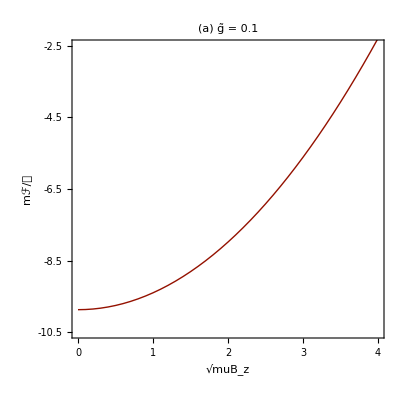

ZeemanFreeA.pdf

```mathematica
gx=0.1;
FRXA=DiscretePlot[FreeEnDensity[π,{0,0,B},gx N[√(2π)]1.58345],{B,0,4,0.1},AspectRatio->1,Joined->True,Filling->None,PlotStyle->Directive[RGBColor[148/255,17/255,0],Thick],PlotRange->{{0,4},{-10.5,-2.5}},Frame->True,FrameTicks->{{{-10.5,-8.5,-6.5,-4.5,-2.5},None},{{0,1,2,3,4},None}},FrameTicksStyle-> Directive[FontSize-> 20,FontFamily -> "Latin Modern Roman",FontColor->Black],
FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->{Style["√muB_z",FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontSize->25,FontColor->Black],Style["mℱ/𝒱",FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontSize->25,FontColor->Black]},PlotLabel->Row[{Style["(a) ",FontSlant->Plain,FontFamily -> "Latin Modern Roman",FontSize->30,FontColor->Black],Style["g̃ = "<>ToString[gx],FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontSize->30,FontColor->Black]}]]
Export["ZeemanFreeA.pdf",FRXA]
```

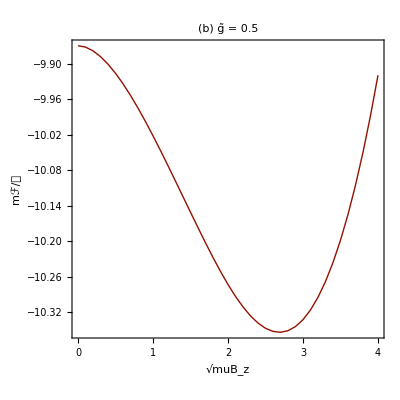

ZeemanFreeB.pdf

```mathematica
gx=0.5;
FRXB=DiscretePlot[FreeEnDensity[π,{0,0,B},gx N[√(2π)]1.58345],{B,0,4,0.1},AspectRatio->1,Joined->True,Filling->None,PlotStyle->Directive[RGBColor[148/255,17/255,0],Thick],PlotRange->{{0,4},All},Frame->True,FrameTicksStyle-> Directive[FontSize-> 20,FontFamily -> "Latin Modern Roman",FontColor->Black],FrameTicks->{{All,None},{All,None}},
FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->{Style["√muB_z",FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontSize->25,FontColor->Black],Style["mℱ/𝒱",FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontSize->25,FontColor->Black]},PlotLabel->Row[{Style["(b) ",FontSlant->Plain,FontFamily -> "Latin Modern Roman",FontSize->30,FontColor->Black],Style["g̃ = "<>ToString[gx],FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontSize->30,FontColor->Black]}]]
Export["ZeemanFreeB.pdf",FRXB]
```

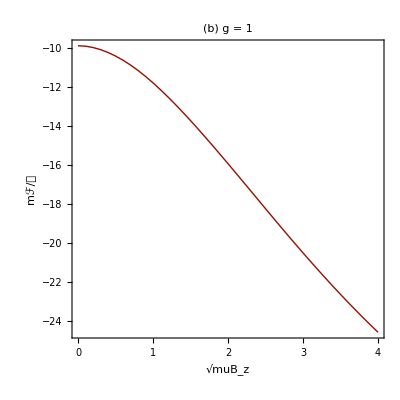

ZeemanFreeB.pdf

```mathematica
gx=1;
FRXB=DiscretePlot[FreeEnDensity[π,{0,0,B},gx N[√(2π)]1.58345],{B,0,4,0.1},AspectRatio->1,Joined->True,Filling->None,PlotStyle->Directive[RGBColor[148/255,17/255,0],Thick],PlotRange->{{0,4},All},Frame->True,FrameTicksStyle-> Directive[FontSize-> 20,FontFamily -> "Latin Modern Roman",FontColor->Black],FrameTicks->{{All,None},{All,None}},
FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->{Style["√muB_z",FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontSize->25,FontColor->Black],Style["mℱ/𝒱",FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontSize->25,FontColor->Black]},PlotLabel->Row[{Style["(b) ",FontSlant->Plain,FontFamily -> "Latin Modern Roman",FontSize->30,FontColor->Black],Style["g = "<>ToString[gx],FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontSize->30,FontColor->Black]}]]
Export["ZeemanFreeB.pdf",FRXB]
```

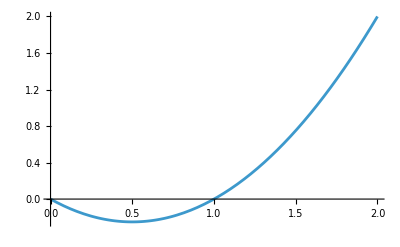

```mathematica
Plot[-x+x^2,{x,0,2}]
```

```mathematica
DisC[FreeEnDensity[1,{0,0,B},1],{B,0,1}]
```

DisC[1/2 {0,0,{{0,0,1/4,0,0},{0,0,0,1/4,-(√3)/4},{-1/4,0,0,0,0},{0,-1/4,0,0,0},{0,(√3)/4,0,0,0}}}.{0,0,{{0,0,1/4,0,0},{0,0,0,1/4,-(√3)/4},{-1/4,0,0,0,0},{0,-1/4,0,0,0},{0,(√3)/4,0,0,0}}}+1/(8 π^3)NIntegrate[EigS[{kx$26571,ky$26571,kz$26571},{Hx$26571,Hy$26571,Hz$26571},1].Fermi/@EigS[{kx$26571,ky$26571,kz$26571},{Hx$26571,Hy$26571,Hz$26571},1],{kx$26571,-1,1},{ky$26571,-1,1},{kz$26571,-1,1}],{{{0,0,1/4,0,0},{0,0,0,1/4,-(√3)/4},{-1/4,0,0,0,0},{0,-1/4,0,0,0},{0,(√3)/4,0,0,0}},0,1}]

8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                      4                 8                 2         2                  6         2                4                  4         4                  2         6                 8                 2         2                  6         2                 2         2                  4         2         2                  2         4         2                  6         2                 4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 2                2                2                           4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                  8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                      4                 8                 2         2                  6         2                4                  4         4                  2         6                 8                 2         2                  6         2                 2         2                  4         2         2                  2         4         2                  6         2                 4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 2                2                2                           4                2         2               4                2         2                2         2               4    2     4                        4                 8                 2         2                  6         2                 4                  4         4                  2         6                 8                 2         2                  6         2                 2         2                  4         2         2                  2         4         2                  6         2                  4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 2                2                 2                           4                2         2               4                2         2                2         2               4    2     4                        4                 8                 2         2                  6         2                4                  4         4                  2         6                 8                 2         2                  6         2                 2         2                  4         2         2                  2         4         2                  6         2                 4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 2                2                2                           4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                  8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                      4                 8                 2         2                  6         2                4                  4         4                  2         6                 8                 2         2                  6         2                 2         2                  4         2         2                  2         4         2                  6         2                 4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 2                2                2                           4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                  8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                        4                 8                 2         2                  6         2                 4                  4         4                  2         6                 8                 2         2                  6         2                 2         2                  4         2         2                  2         4         2                  6         2                  4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 2                2                 2                           4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4
Root::npoly : {{65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 2304 + 8192 kx$26571  + 65536 kx$26571  + 16384 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 8192 ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  - 32768 kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 32768 ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 40960 kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (2048 kx$26571  + 2048 ky$26571  - 4096 kz$26571 ) #1 + (-160 - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 }, {65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 2304 + 8192 kx$26571  + 65536 kx$26571  + 16384 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 8192 ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  - 32768 kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 32768 ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 40960 kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (2048 kx$26571  + 2048 ky$26571  - 4096 kz$26571 ) #1 + (-160 - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 20736 + 24576 kx$26571  + 65536 kx$26571  + 49152 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 24576 ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  - 98304 kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 98304 ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 122880 kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (6144 kx$26571  + 6144 ky$26571  - 12288 kz$26571 ) #1 + (-480 - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 }, {2304 + 8192 kx$26571  + 65536 kx$26571  + 16384 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 8192 ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  - 32768 kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 32768 ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 40960 kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (2048 kx$26571  + 2048 ky$26571  - 4096 kz$26571 ) #1 + (-160 - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 }, {65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 2304 + 8192 kx$26571  + 65536 kx$26571  + 16384 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 8192 ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  - 32768 kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 32768 ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 40960 kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (2048 kx$26571  + 2048 ky$26571  - 4096 kz$26571 ) #1 + (-160 - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 }, {65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 20736 + 24576 kx$26571  + 65536 kx$26571  + 49152 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 24576 ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  - 98304 kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 98304 ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 122880 kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (6144 kx$26571  + 6144 ky$26571  - 12288 kz$26571 ) #1 + (-480 - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 }} is not a polynomial in #1.

General::stop: Further output of Root::npoly will be suppressed during this calculation.

8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                      4                 8                 2         2                  6         2                4                  4         4                  2         6                 8                 2         2                  6         2                 2         2                  4         2         2                  2         4         2                  6         2                 4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 2                2                2                           4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                  8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                      4                 8                 2         2                  6         2                4                  4         4                  2         6                 8                 2         2                  6         2                 2         2                  4         2         2                  2         4         2                  6         2                 4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 2                2                2                           4                2         2               4                2         2                2         2               4    2     4                        4                 8                 2         2                  6         2                 4                  4         4                  2         6                 8                 2         2                  6         2                 2         2                  4         2         2                  2         4         2                  6         2                  4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 2                2                 2                           4                2         2               4                2         2                2         2               4    2     4                        4                 8                 2         2                  6         2                4                  4         4                  2         6                 8                 2         2                  6         2                 2         2                  4         2         2                  2         4         2                  6         2                 4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 2                2                2                           4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                  8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                      4                 8                 2         2                  6         2                4                  4         4                  2         6                 8                 2         2                  6         2                 2         2                  4         2         2                  2         4         2                  6         2                 4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 2                2                2                           4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                  8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                        4                 8                 2         2                  6         2                 4                  4         4                  2         6                 8                 2         2                  6         2                 2         2                  4         2         2                  2         4         2                  6         2                  4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 2                2                 2                           4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4
Root::npoly : {{65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 2304 + 8192 kx$26571  + 65536 kx$26571  + 16384 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 8192 ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  - 32768 kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 32768 ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 40960 kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (2048 kx$26571  + 2048 ky$26571  - 4096 kz$26571 ) #1 + (-160 - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 }, {65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 2304 + 8192 kx$26571  + 65536 kx$26571  + 16384 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 8192 ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  - 32768 kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 32768 ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 40960 kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (2048 kx$26571  + 2048 ky$26571  - 4096 kz$26571 ) #1 + (-160 - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 20736 + 24576 kx$26571  + 65536 kx$26571  + 49152 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 24576 ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  - 98304 kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 98304 ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 122880 kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (6144 kx$26571  + 6144 ky$26571  - 12288 kz$26571 ) #1 + (-480 - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 }, {2304 + 8192 kx$26571  + 65536 kx$26571  + 16384 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 8192 ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  - 32768 kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 32768 ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 40960 kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (2048 kx$26571  + 2048 ky$26571  - 4096 kz$26571 ) #1 + (-160 - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 }, {65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 2304 + 8192 kx$26571  + 65536 kx$26571  + 16384 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 8192 ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  - 32768 kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 32768 ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 40960 kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (2048 kx$26571  + 2048 ky$26571  - 4096 kz$26571 ) #1 + (-160 - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 }, {65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 20736 + 24576 kx$26571  + 65536 kx$26571  + 49152 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 24576 ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  - 98304 kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 98304 ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 122880 kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (6144 kx$26571  + 6144 ky$26571  - 12288 kz$26571 ) #1 + (-480 - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 }} is not a polynomial in #1.

4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4                                           4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4                                 4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4                                           4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4                                 4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4                                           4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4                                 4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4                                           4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4
NIntegrate::inumr : The integrand 0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 1] (1 - UnitStep[0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 1]]) + 0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 2] (1 - UnitStep[0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 2]]) + 0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 3] (1 - UnitStep[0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 3]]) + 0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 4] (1 - UnitStep[0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 4]]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1, 1}, {-1, 1}, {-1, 1}}.
                                                                                                                    4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                   4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                                                                         4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                   4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                                                                         4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                   4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                                                                         4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                   4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4

Dot::rect: Nonrectangular tensor encountered.

8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                      4                 8                 2         2                  6         2                4                  4         4                  2         6                 8                 2         2                  6         2                 2         2                  4         2         2                  2         4         2                  6         2                 4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 2                2                2                           4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                  8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                      4                 8                 2         2                  6         2                4                  4         4                  2         6                 8                 2         2                  6         2                 2         2                  4         2         2                  2         4         2                  6         2                 4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 2                2                2                           4                2         2               4                2         2                2         2               4    2     4                        4                 8                 2         2                  6         2                 4                  4         4                  2         6                 8                 2         2                  6         2                 2         2                  4         2         2                  2         4         2                  6         2                  4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 2                2                 2                           4                2         2               4                2         2                2         2               4    2     4                        4                 8                 2         2                  6         2                4                  4         4                  2         6                 8                 2         2                  6         2                 2         2                  4         2         2                  2         4         2                  6         2                 4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 2                2                2                           4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                  8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                      4                 8                 2         2                  6         2                4                  4         4                  2         6                 8                 2         2                  6         2                 2         2                  4         2         2                  2         4         2                  6         2                 4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 2                2                2                           4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                  8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                        4                 8                 2         2                  6         2                 4                  4         4                  2         6                 8                 2         2                  6         2                 2         2                  4         2         2                  2         4         2                  6         2                  4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 2                2                 2                           4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4
Root::npoly : {{65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 2304 + 8192 kx$26571  + 65536 kx$26571  + 16384 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 8192 ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  - 32768 kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 32768 ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 40960 kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (2048 kx$26571  + 2048 ky$26571  - 4096 kz$26571 ) #1 + (-160 - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 }, {65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 2304 + 8192 kx$26571  + 65536 kx$26571  + 16384 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 8192 ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  - 32768 kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 32768 ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 40960 kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (2048 kx$26571  + 2048 ky$26571  - 4096 kz$26571 ) #1 + (-160 - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 20736 + 24576 kx$26571  + 65536 kx$26571  + 49152 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 24576 ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  - 98304 kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 98304 ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 122880 kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (6144 kx$26571  + 6144 ky$26571  - 12288 kz$26571 ) #1 + (-480 - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 }, {2304 + 8192 kx$26571  + 65536 kx$26571  + 16384 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 8192 ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  - 32768 kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 32768 ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 40960 kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (2048 kx$26571  + 2048 ky$26571  - 4096 kz$26571 ) #1 + (-160 - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 }, {65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 2304 + 8192 kx$26571  + 65536 kx$26571  + 16384 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 8192 ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  - 32768 kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 32768 ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 40960 kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (2048 kx$26571  + 2048 ky$26571  - 4096 kz$26571 ) #1 + (-160 - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 }, {65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 20736 + 24576 kx$26571  + 65536 kx$26571  + 49152 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 24576 ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  - 98304 kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 98304 ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 122880 kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (6144 kx$26571  + 6144 ky$26571  - 12288 kz$26571 ) #1 + (-480 - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 }} is not a polynomial in #1.

4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4                                           4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4                                 4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4                                           4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4                                 4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4                                           4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4                                 4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4                                           4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4
NIntegrate::inumr : The integrand 0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 1] (1 - UnitStep[0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 1]]) + 0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 2] (1 - UnitStep[0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 2]]) + 0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 3] (1 - UnitStep[0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 3]]) + 0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 4] (1 - UnitStep[0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 4]]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1, 1}, {-1, 1}, {-1, 1}}.
                                                                                                                    4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                   4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                                                                         4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                   4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                                                                         4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                   4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                                                                         4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                   4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4

8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                      4                 8                 2         2                  6         2                4                  4         4                  2         6                 8                 2         2                  6         2                 2         2                  4         2         2                  2         4         2                  6         2                 4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 2                2                2                           4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                  8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                      4                 8                 2         2                  6         2                4                  4         4                  2         6                 8                 2         2                  6         2                 2         2                  4         2         2                  2         4         2                  6         2                 4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 2                2                2                           4                2         2               4                2         2                2         2               4    2     4                        4                 8                 2         2                  6         2                 4                  4         4                  2         6                 8                 2         2                  6         2                 2         2                  4         2         2                  2         4         2                  6         2                  4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 2                2                 2                           4                2         2               4                2         2                2         2               4    2     4                        4                 8                 2         2                  6         2                4                  4         4                  2         6                 8                 2         2                  6         2                 2         2                  4         2         2                  2         4         2                  6         2                 4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 2                2                2                           4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                  8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                      4                 8                 2         2                  6         2                4                  4         4                  2         6                 8                 2         2                  6         2                 2         2                  4         2         2                  2         4         2                  6         2                 4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 2                2                2                           4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                  8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                        4                 8                 2         2                  6         2                 4                  4         4                  2         6                 8                 2         2                  6         2                 2         2                  4         2         2                  2         4         2                  6         2                  4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 2                2                 2                           4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4
Root::npoly : {{65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 2304 + 8192 kx$26571  + 65536 kx$26571  + 16384 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 8192 ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  - 32768 kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 32768 ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 40960 kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (2048 kx$26571  + 2048 ky$26571  - 4096 kz$26571 ) #1 + (-160 - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 }, {65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 2304 + 8192 kx$26571  + 65536 kx$26571  + 16384 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 8192 ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  - 32768 kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 32768 ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 40960 kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (2048 kx$26571  + 2048 ky$26571  - 4096 kz$26571 ) #1 + (-160 - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 20736 + 24576 kx$26571  + 65536 kx$26571  + 49152 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 24576 ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  - 98304 kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 98304 ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 122880 kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (6144 kx$26571  + 6144 ky$26571  - 12288 kz$26571 ) #1 + (-480 - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 }, {2304 + 8192 kx$26571  + 65536 kx$26571  + 16384 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 8192 ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  - 32768 kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 32768 ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 40960 kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (2048 kx$26571  + 2048 ky$26571  - 4096 kz$26571 ) #1 + (-160 - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 }, {65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 2304 + 8192 kx$26571  + 65536 kx$26571  + 16384 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 8192 ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  - 32768 kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 32768 ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 40960 kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (2048 kx$26571  + 2048 ky$26571  - 4096 kz$26571 ) #1 + (-160 - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 }, {65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 20736 + 24576 kx$26571  + 65536 kx$26571  + 49152 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 24576 ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  - 98304 kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 98304 ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 122880 kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (6144 kx$26571  + 6144 ky$26571  - 12288 kz$26571 ) #1 + (-480 - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 }} is not a polynomial in #1.

4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4                                           4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4                                 4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4                                           4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4                                 4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4                                           4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4                                 4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4                                           4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4
NIntegrate::inumr : The integrand 0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 1] (1 - UnitStep[0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 1]]) + 0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 2] (1 - UnitStep[0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 2]]) + 0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 3] (1 - UnitStep[0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 3]]) + 0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 4] (1 - UnitStep[0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 4]]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1, 1}, {-1, 1}, {-1, 1}}.
                                                                                                                    4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                   4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                                                                         4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                   4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                                                                         4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                   4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                                                                         4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                   4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                      4                 8                 2         2                  6         2                4                  4         4                  2         6                 8                 2         2                  6         2                 2         2                  4         2         2                  2         4         2                  6         2                 4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 2                2                2                           4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                  8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                      4                 8                 2         2                  6         2                4                  4         4                  2         6                 8                 2         2                  6         2                 2         2                  4         2         2                  2         4         2                  6         2                 4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 2                2                2                           4                2         2               4                2         2                2         2               4    2     4                        4                 8                 2         2                  6         2                 4                  4         4                  2         6                 8                 2         2                  6         2                 2         2                  4         2         2                  2         4         2                  6         2                  4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 2                2                 2                           4                2         2               4                2         2                2         2               4    2     4                        4                 8                 2         2                  6         2                4                  4         4                  2         6                 8                 2         2                  6         2                 2         2                  4         2         2                  2         4         2                  6         2                 4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 2                2                2                           4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                  8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                      4                 8                 2         2                  6         2                4                  4         4                  2         6                 8                 2         2                  6         2                 2         2                  4         2         2                  2         4         2                  6         2                 4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 2                2                2                           4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                  8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                        4                 8                 2         2                  6         2                 4                  4         4                  2         6                 8                 2         2                  6         2                 2         2                  4         2         2                  2         4         2                  6         2                  4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 2                2                 2                           4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4
Root::npoly : {{65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 2304 + 8192 kx$26571  + 65536 kx$26571  + 16384 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 8192 ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  - 32768 kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 32768 ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 40960 kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (2048 kx$26571  + 2048 ky$26571  - 4096 kz$26571 ) #1 + (-160 - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 }, {65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 2304 + 8192 kx$26571  + 65536 kx$26571  + 16384 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 8192 ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  - 32768 kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 32768 ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 40960 kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (2048 kx$26571  + 2048 ky$26571  - 4096 kz$26571 ) #1 + (-160 - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 20736 + 24576 kx$26571  + 65536 kx$26571  + 49152 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 24576 ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  - 98304 kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 98304 ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 122880 kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (6144 kx$26571  + 6144 ky$26571  - 12288 kz$26571 ) #1 + (-480 - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 }, {2304 + 8192 kx$26571  + 65536 kx$26571  + 16384 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 8192 ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  - 32768 kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 32768 ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 40960 kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (2048 kx$26571  + 2048 ky$26571  - 4096 kz$26571 ) #1 + (-160 - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 }, {65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 2304 + 8192 kx$26571  + 65536 kx$26571  + 16384 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 8192 ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  - 32768 kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 32768 ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 40960 kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (2048 kx$26571  + 2048 ky$26571  - 4096 kz$26571 ) #1 + (-160 - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 }, {65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 20736 + 24576 kx$26571  + 65536 kx$26571  + 49152 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 24576 ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  - 98304 kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 98304 ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 122880 kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (6144 kx$26571  + 6144 ky$26571  - 12288 kz$26571 ) #1 + (-480 - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 }} is not a polynomial in #1.

4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4                                           4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4                                 4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4                                           4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4                                 4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4                                           4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4                                 4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4                                           4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4
NIntegrate::inumr : The integrand 0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 1] (1 - UnitStep[0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 1]]) + 0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 2] (1 - UnitStep[0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 2]]) + 0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 3] (1 - UnitStep[0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 3]]) + 0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 4] (1 - UnitStep[0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 4]]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1, 1}, {-1, 1}, {-1, 1}}.
                                                                                                                    4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                   4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                                                                         4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                   4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                                                                         4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                   4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                                                                         4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                   4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4

8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                      4                 8                 2         2                  6         2                4                  4         4                  2         6                 8                 2         2                  6         2                 2         2                  4         2         2                  2         4         2                  6         2                 4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 2                2                2                           4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                  8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                      4                 8                 2         2                  6         2                4                  4         4                  2         6                 8                 2         2                  6         2                 2         2                  4         2         2                  2         4         2                  6         2                 4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 2                2                2                           4                2         2               4                2         2                2         2               4    2     4                        4                 8                 2         2                  6         2                 4                  4         4                  2         6                 8                 2         2                  6         2                 2         2                  4         2         2                  2         4         2                  6         2                  4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 2                2                 2                           4                2         2               4                2         2                2         2               4    2     4                        4                 8                 2         2                  6         2                4                  4         4                  2         6                 8                 2         2                  6         2                 2         2                  4         2         2                  2         4         2                  6         2                 4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 2                2                2                           4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                  8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                      4                 8                 2         2                  6         2                4                  4         4                  2         6                 8                 2         2                  6         2                 2         2                  4         2         2                  2         4         2                  6         2                 4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 2                2                2                           4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                  8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                        4                 8                 2         2                  6         2                 4                  4         4                  2         6                 8                 2         2                  6         2                 2         2                  4         2         2                  2         4         2                  6         2                  4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 2                2                 2                           4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4
Root::npoly : {{65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 2304 + 8192 kx$26571  + 65536 kx$26571  + 16384 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 8192 ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  - 32768 kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 32768 ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 40960 kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (2048 kx$26571  + 2048 ky$26571  - 4096 kz$26571 ) #1 + (-160 - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 }, {65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 2304 + 8192 kx$26571  + 65536 kx$26571  + 16384 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 8192 ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  - 32768 kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 32768 ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 40960 kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (2048 kx$26571  + 2048 ky$26571  - 4096 kz$26571 ) #1 + (-160 - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 20736 + 24576 kx$26571  + 65536 kx$26571  + 49152 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 24576 ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  - 98304 kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 98304 ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 122880 kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (6144 kx$26571  + 6144 ky$26571  - 12288 kz$26571 ) #1 + (-480 - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 }, {2304 + 8192 kx$26571  + 65536 kx$26571  + 16384 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 8192 ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  - 32768 kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 32768 ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 40960 kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (2048 kx$26571  + 2048 ky$26571  - 4096 kz$26571 ) #1 + (-160 - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 }, {65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 2304 + 8192 kx$26571  + 65536 kx$26571  + 16384 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 8192 ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  - 32768 kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 32768 ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 40960 kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (2048 kx$26571  + 2048 ky$26571  - 4096 kz$26571 ) #1 + (-160 - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 }, {65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 20736 + 24576 kx$26571  + 65536 kx$26571  + 49152 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 24576 ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  - 98304 kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 98304 ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 122880 kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (6144 kx$26571  + 6144 ky$26571  - 12288 kz$26571 ) #1 + (-480 - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 }} is not a polynomial in #1.

4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4                                           4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4                                 4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4                                           4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4                                 4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4                                           4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4                                 4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4                                           4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4
NIntegrate::inumr : The integrand 0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 1] (1 - UnitStep[0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 1]]) + 0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 2] (1 - UnitStep[0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 2]]) + 0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 3] (1 - UnitStep[0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 3]]) + 0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 4] (1 - UnitStep[0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 4]]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1, 1}, {-1, 1}, {-1, 1}}.
                                                                                                                    4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                   4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                                                                         4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                   4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                                                                         4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                   4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                                                                         4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                   4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4

8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                      4                 8                 2         2                  6         2                4                  4         4                  2         6                 8                 2         2                  6         2                 2         2                  4         2         2                  2         4         2                  6         2                 4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 2                2                2                           4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                  8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                      4                 8                 2         2                  6         2                4                  4         4                  2         6                 8                 2         2                  6         2                 2         2                  4         2         2                  2         4         2                  6         2                 4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 2                2                2                           4                2         2               4                2         2                2         2               4    2     4                        4                 8                 2         2                  6         2                 4                  4         4                  2         6                 8                 2         2                  6         2                 2         2                  4         2         2                  2         4         2                  6         2                  4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 2                2                 2                           4                2         2               4                2         2                2         2               4    2     4                        4                 8                 2         2                  6         2                4                  4         4                  2         6                 8                 2         2                  6         2                 2         2                  4         2         2                  2         4         2                  6         2                 4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 2                2                2                           4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                  8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                      4                 8                 2         2                  6         2                4                  4         4                  2         6                 8                 2         2                  6         2                 2         2                  4         2         2                  2         4         2                  6         2                 4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 2                2                2                           4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                  8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                        4                 8                 2         2                  6         2                 4                  4         4                  2         6                 8                 2         2                  6         2                 2         2                  4         2         2                  2         4         2                  6         2                  4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 2                2                 2                           4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4
Root::npoly : {{65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 2304 + 8192 kx$26571  + 65536 kx$26571  + 16384 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 8192 ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  - 32768 kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 32768 ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 40960 kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (2048 kx$26571  + 2048 ky$26571  - 4096 kz$26571 ) #1 + (-160 - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 }, {65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 2304 + 8192 kx$26571  + 65536 kx$26571  + 16384 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 8192 ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  - 32768 kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 32768 ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 40960 kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (2048 kx$26571  + 2048 ky$26571  - 4096 kz$26571 ) #1 + (-160 - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 20736 + 24576 kx$26571  + 65536 kx$26571  + 49152 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 24576 ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  - 98304 kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 98304 ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 122880 kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (6144 kx$26571  + 6144 ky$26571  - 12288 kz$26571 ) #1 + (-480 - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 }, {2304 + 8192 kx$26571  + 65536 kx$26571  + 16384 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 8192 ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  - 32768 kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 32768 ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 40960 kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (2048 kx$26571  + 2048 ky$26571  - 4096 kz$26571 ) #1 + (-160 - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 }, {65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 2304 + 8192 kx$26571  + 65536 kx$26571  + 16384 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 8192 ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  - 32768 kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 32768 ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 40960 kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (2048 kx$26571  + 2048 ky$26571  - 4096 kz$26571 ) #1 + (-160 - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 }, {65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 20736 + 24576 kx$26571  + 65536 kx$26571  + 49152 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 24576 ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  - 98304 kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 98304 ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 122880 kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (6144 kx$26571  + 6144 ky$26571  - 12288 kz$26571 ) #1 + (-480 - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 }} is not a polynomial in #1.

4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4                                           4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4                                 4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4                                           4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4                                 4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4                                           4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4                                 4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4                                           4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4
NIntegrate::inumr : The integrand 0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 1] (1 - UnitStep[0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 1]]) + 0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 2] (1 - UnitStep[0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 2]]) + 0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 3] (1 - UnitStep[0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 3]]) + 0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 4] (1 - UnitStep[0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 4]]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1, 1}, {-1, 1}, {-1, 1}}.
                                                                                                                    4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                   4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                                                                         4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                   4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                                                                         4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                   4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                                                                         4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                   4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4

8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                      4                 8                 2         2                  6         2                4                  4         4                  2         6                 8                 2         2                  6         2                 2         2                  4         2         2                  2         4         2                  6         2                 4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 2                2                2                           4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                  8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                      4                 8                 2         2                  6         2                4                  4         4                  2         6                 8                 2         2                  6         2                 2         2                  4         2         2                  2         4         2                  6         2                 4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 2                2                2                           4                2         2               4                2         2                2         2               4    2     4                        4                 8                 2         2                  6         2                 4                  4         4                  2         6                 8                 2         2                  6         2                 2         2                  4         2         2                  2         4         2                  6         2                  4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 2                2                 2                           4                2         2               4                2         2                2         2               4    2     4                        4                 8                 2         2                  6         2                4                  4         4                  2         6                 8                 2         2                  6         2                 2         2                  4         2         2                  2         4         2                  6         2                 4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 2                2                2                           4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                  8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                      4                 8                 2         2                  6         2                4                  4         4                  2         6                 8                 2         2                  6         2                 2         2                  4         2         2                  2         4         2                  6         2                 4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 2                2                2                           4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                  8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                        4                 8                 2         2                  6         2                 4                  4         4                  2         6                 8                 2         2                  6         2                 2         2                  4         2         2                  2         4         2                  6         2                  4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 2                2                 2                           4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4                8                  6         2                  4         4                  2         6                 8                  6         2                  4         2         2                  2         4         2                  6         2                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8                 4                2         2               4                2         2                2         2               4    2     4
Root::npoly : {{65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 2304 + 8192 kx$26571  + 65536 kx$26571  + 16384 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 8192 ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  - 32768 kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 32768 ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 40960 kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (2048 kx$26571  + 2048 ky$26571  - 4096 kz$26571 ) #1 + (-160 - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 }, {65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 2304 + 8192 kx$26571  + 65536 kx$26571  + 16384 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 8192 ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  - 32768 kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 32768 ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 40960 kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (2048 kx$26571  + 2048 ky$26571  - 4096 kz$26571 ) #1 + (-160 - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 20736 + 24576 kx$26571  + 65536 kx$26571  + 49152 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 24576 ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  - 98304 kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 98304 ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 122880 kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (6144 kx$26571  + 6144 ky$26571  - 12288 kz$26571 ) #1 + (-480 - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 }, {2304 + 8192 kx$26571  + 65536 kx$26571  + 16384 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 8192 ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  - 32768 kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 32768 ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 40960 kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (2048 kx$26571  + 2048 ky$26571  - 4096 kz$26571 ) #1 + (-160 - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 }, {65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 2304 + 8192 kx$26571  + 65536 kx$26571  + 16384 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 8192 ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  - 32768 kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 32768 ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 40960 kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (2048 kx$26571  + 2048 ky$26571  - 4096 kz$26571 ) #1 + (-160 - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 }, {65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 20736 + 24576 kx$26571  + 65536 kx$26571  + 49152 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 24576 ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  - 98304 kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 98304 ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 122880 kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (6144 kx$26571  + 6144 ky$26571  - 12288 kz$26571 ) #1 + (-480 - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 , 65536 kx$26571  + 262144 kx$26571  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 262144 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (-512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1 }} is not a polynomial in #1.

4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4                                           4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4                                 4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4                                           4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4                                 4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4                                           4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4                                 4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4                                           4  4           4  2  2           4  4           4  2         1                   1    1               1                      1                 Sqrt[3]           2            4  2         1                   1    1               1                      1                 Sqrt[3]           2           4         1                   1    1               1                      1                 Sqrt[3]           4           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                 8            2             3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                      3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         6                 8            2           1                   1    1               1                      1                 Sqrt[3]                    3                     2           1                   1    1               1                      1                 Sqrt[3]                    2                              2           1                   1    1               1                      1                 Sqrt[3]                             2                     2           1                   1    1               1                      1                 Sqrt[3]                    3                    2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  6         2            2                               2           2  2         2         2           2  2         2         2           2         1                   1    1               1                      1                 Sqrt[3]           2         2         2                  4         2         2                  2         4         2                  6         2            2           1                   1    1               1                      1                 Sqrt[3]                             3            2           1                   1    1               1                      1                 Sqrt[3]                             3           2  2         4           2  2         4           2         1                   1    1               1                      1                 Sqrt[3]           2         4                  4         4                  2         2         4                  4         4                  2         6                  2         6                 8           2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2                                2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2           2           1                   1    1               1                      1                 Sqrt[3]                                        2           1                   1    1               1                      1                 Sqrt[3]                                       2  2         2          2  2         2          2         1                   1    1               1                      1                 Sqrt[3]           2         2               2  2         2  2         2         1                   1    1               1                      1                 Sqrt[3]           2               4                2         2               4                2         2                2         2               4    2     4
NIntegrate::inumr : The integrand 0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 1] (1 - UnitStep[0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 1]]) + 0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 2] (1 - UnitStep[0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 2]]) + 0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 3] (1 - UnitStep[0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 3]]) + 0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 4] (1 - UnitStep[0.03125 Root[589824 1  0  - 917504 1  0  0  + 589824 1  0  - 917504 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 1179648 1  0  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  + 589824 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 655360 1  0  kx$26571  + 131072 1  0  kx$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  + 65536 kx$26571  + 1572864 1  0 0 kx$26571  ky$26571 - 524288 1  0  kx$26571  ky$26571  - 524288 1  0  kx$26571  ky$26571  + 262144 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  ky$26571  + 262144 kx$26571  ky$26571  - 1572864 1  0 0 kx$26571 ky$26571  + 131072 1  0  ky$26571  - 655360 1  0  ky$26571  + 131072 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  + 393216 kx$26571  ky$26571  + 262144 kx$26571  ky$26571  + 65536 ky$26571  + 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571  ky$26571 kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 ky$26571  kz$26571 - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571  kz$26571 - 524288 1  0  kx$26571  kz$26571  + 262144 1  0  kx$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  kz$26571  + 262144 kx$26571  kz$26571  - 1572864 1  0 0 kx$26571 ky$26571 kz$26571  + 262144 1  0  ky$26571  kz$26571  - 524288 1  0  ky$26571  kz$26571  - 524288 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 262144 ky$26571  kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571  - 1572864 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571  + 131072 1  0  kz$26571  + 131072 1  0  kz$26571  - 655360 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571  + 393216 kx$26571  kz$26571  + 786432 kx$26571  ky$26571  kz$26571  + 393216 ky$26571  kz$26571  + 262144 kx$26571  kz$26571  + 262144 ky$26571  kz$26571  + 65536 kz$26571  + (65536 1  0  kx$26571  + 32768 1  0  kx$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kx$26571  - 196608 1  0 0 kx$26571 ky$26571 - 32768 1  0  ky$26571  - 65536 1  0  ky$26571  + 32768 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  ky$26571  - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} kx$26571 kz$26571 - 196608 1  0 {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}} ky$26571 kz$26571 - 32768 1  0  kz$26571  + 32768 1  0  kz$26571  - 65536 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  kz$26571 ) #1 + (-2560 1  0  - 2560 1  0  - 2560 1  {{0, 0, -, 0, 0}, {0, 0, 0, -, -(-) Sqrt[3]}, {-(-), 0, 0, 0, 0}, {0, -(-), 0, 0, 0}, {0, -------, 0, 0, 0}}  - 512 kx$26571  - 1024 kx$26571  ky$26571  - 512 ky$26571  - 1024 kx$26571  kz$26571  - 1024 ky$26571  kz$26571  - 512 kz$26571 ) #1  + #1  & , 4]]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1, 1}, {-1, 1}, {-1, 1}}.
                                                                                                                    4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                   4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                                                                         4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                   4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                                                                         4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                   4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                                                                         4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                   4                   4    4               4                      4                    4                                        4                   4    4               4                      4                    4                                    4                   4    4               4                      4                    4                                                                                      4                   4    4               4                      4                    4                                                                                                                                                                          4                   4    4               4                      4                    4                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                             4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                  4                   4    4               4                      4                    4                                                                                                                            4                   4    4               4                      4                    4                                                                                                                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                      4                   4    4               4                      4                    4                                                         4                   4    4               4                      4                    4                                                                                                        4                   4    4               4                      4                    4                                                                                                                                                                                                                                                                           4                   4    4               4                      4                    4                                                                                                                               4                   4    4               4                      4                    4                                                4                   4    4               4                      4                    4                                                       4                   4    4               4                      4                    4                                                                                                    4                   4    4               4                      4                    4                                                                            4                   4    4               4                      4                    4

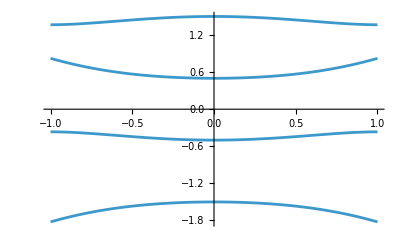

```mathematica
Plot[EigS[{kx,0,0},{0,0,1},1],{kx,-1,1}]
```

```mathematica
RGBColor[255/255,194/255,10/255]
```

RGBColor[1, Rational[194, 255], Rational[2, 51]]

```mathematica
RGBColor[12/255,123/255,220/255]
```

RGBColor[Rational[4, 85], Rational[41, 85], Rational[44, 51]]

```mathematica
SemiMetal=Plot3D[{0,EigS[{0,ky,kz},{0,0,0},1]},{ky,-1,1},{kz,-1,1},BoxRatios->{1, 1, 1},PlotStyle->{{RGBColor[255/255,194/255,10/255],Opacity[0.25]},{RGBColor[12/255,123/255,220/255],Opacity[0.75]}},Mesh->None,TicksStyle-> Directive[FontSize-> 20,FontFamily -> "Latin Modern Roman",FontColor->Black],AxesStyle->Directive[Black,Thickness[0.005]],
AxesStyle->Directive[Black,Thickness[0.005]],AxesLabel->{Style["k_y",FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontSize->25,FontColor->Black],Style["k_z",FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontSize->25,FontColor->Black],Style["E",FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontSize->25,FontColor->Black]},PlotLabel->Style["⟨B⃗⟩ = 0",FontSlant->Italic,FontFamily->"Latin Modern Roman",FontSize->30,FontColor->Black],ViewPoint->{1.2, -2.4, 1.2},ImageSize->500,Lighting->{"Ambient",White,{1.2, -2.4, 1.2}}]
Export["SemiMetal.pdf",SemiMetal]
```

-Graphics3D-

SemiMetal.pdf

```mathematica
BMetal=Plot3D[{0,EigS[{0,ky,kz},{0,0,1},1]},{ky,-2,2},{kz,-2,2},BoxRatios->{1, 1, 1},PlotStyle->{{RGBColor[255/255,194/255,10/255],Opacity[0.25]},{RGBColor[12/255,123/255,220/255],Opacity[0.75]}},Mesh->None,TicksStyle-> Directive[FontSize-> 20,FontFamily -> "Latin Modern Roman",FontColor->Black],AxesStyle->Directive[Black,Thickness[0.005]],
AxesStyle->Directive[Black,Thickness[0.005]],AxesLabel->{Style["k_y",FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontSize->25,FontColor->Black],Style["k_z",FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontSize->25,FontColor->Black],Style["E",FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontSize->25,FontColor->Black]},PlotLabel->Style["⟨B⃗⟩ ≠ 0",FontSlant->Italic,FontFamily->"Latin Modern Roman",FontSize->30,FontColor->Black],ViewPoint->{1.2, -2.4, 1.2},ImageSize->500,Lighting->{"Ambient",White,{1.2, -2.4, 1.2}}]
Export["BMetal.pdf",BMetal]
```

-Graphics3D-

BMetal.pdf

## Landau levels

```mathematica
DeclareNonCommutative[a,a†,q,qs,p]
```

```mathematica
Commutator[a,a†]=1
```

1

Set::write: Tag Commutator in Commutator[a, ConjugateTranspose[a]] is Protected.

```mathematica
p=(a-a†)/(√2 I)
```

-(ⅈ (a-ConjugateTranspose[a]))/(√2)

```mathematica
q=(a+a†)/(√2)
```

(a+ConjugateTranspose[a])/(√2)

```mathematica
ClearAll[B]
```

```mathematica
iqs=I e B q
```

(ⅈ B e (a+ConjugateTranspose[a]))/(√2)

```mathematica
Calc[Commutator[q,p]]
```

-(-(ⅈ (a-ConjugateTranspose[a]))/(√2))**(a+ConjugateTranspose[a])/(√2)+(a+ConjugateTranspose[a])/(√2)**(-(ⅈ (a-ConjugateTranspose[a]))/(√2))

```mathematica
Collect2[DotSimplify[Calc[DotSimplify[DotExpand[-(L[i,1,1](I p).(I p)+L[i,1,2](I p).iqs+L[i,1,3](I p) (I kz)+L[i,1,2]iqs.(I p)+L[i,2,2]iqs.iqs+L[i,2,3]iqs (I kz)+L[i,1,3](I kz)(I p)+L[i,2,3](I kz)iqs+L[i,3,3](I kz)(I kz))]]]],{a,ConjugateTranspose[a],ConjugateTranspose[a].a,ConjugateTranspose[a].ConjugateTranspose[a],a.a,1}]
```

-1/2 ConjugateTranspose[a].ConjugateTranspose[a] (L[i,1,1]-2 ⅈ B e L[i,1,2]-B^2 e^2 L[i,2,2])-1/2 a.a (L[i,1,1]+2 ⅈ B e L[i,1,2]-B^2 e^2 L[i,2,2])+1/2 a.ConjugateTranspose[a] (L[i,1,1]+B^2 e^2 L[i,2,2])+1/2 ConjugateTranspose[a].a (L[i,1,1]+B^2 e^2 L[i,2,2])+√2 a kz (-ⅈ L[i,1,3]+B e L[i,2,3])+√2 kz ConjugateTranspose[a] (ⅈ L[i,1,3]+B e L[i,2,3])+kz^2 L[i,3,3]

```mathematica
Collect2[DotSimplify[Calc[DotSimplify[DotExpand[-(L[i,1,1](I p).(I p)+L[i,1,2](I p).iqs+L[i,1,3](I p) (I kz)+L[i,1,2]iqs.(I p)+L[i,2,2]iqs.iqs+L[i,2,3]iqs (I kz)+L[i,1,3](I kz)(I p)+L[i,2,3](I kz)iqs+L[i,3,3](I kz)(I kz))]]]],{a,ConjugateTranspose[a],ConjugateTranspose[a].a,ConjugateTranspose[a].ConjugateTranspose[a],a.a,1}]//TraditionalForm
```

-1/2 ConjugateTranspose[a].ConjugateTranspose[a] (-B^2 e^2 L(i,2,2)-2 ⅈ B e L(i,1,2)+L(i,1,1))+1/2 a.ConjugateTranspose[a] (B^2 e^2 L(i,2,2)+L(i,1,1))+1/2 ConjugateTranspose[a].a (B^2 e^2 L(i,2,2)+L(i,1,1))-1/2 a.a (-B^2 e^2 L(i,2,2)+2 ⅈ B e L(i,1,2)+L(i,1,1))+√2 kz ConjugateTranspose[a] (B e L(i,2,3)+ⅈ L(i,1,3))+√2 a kz (B e L(i,2,3)-ⅈ L(i,1,3))+kz^2 L(i,3,3)

```mathematica
LandauHam[m_,n_,e_,B_,kz_]:=Module[{a,b,bstar,c,cstar,d,i},a= Sum[(Λ[[i,1,1]]+B^2 e^2 Λ[[i,2,2]])Γ[[i]],{i,1,5}];b=Sum[(1/2  (-Λ[[i,1,1]]+2 ⅈ B e Λ[[i,1,2]]+B^2 e^2 Λ[[i,2,2]]))Γ[[i]],{i,1,5}];bstar=Sum[(1/2 (-Λ[[i,1,1]]-2 ⅈ B e Λ[[i,1,2]]+B^2 e^2 Λ[[i,2,2]]))Γ[[i]],{i,1,5}];
c=Sum[I(-√2  kz (Λ[[i,1,3]]+ⅈ B e Λ[[i,2,3]]))Γ[[i]],{i,1,5}];
cstar=Sum[I(√2 kz  (Λ[[i,1,3]]-ⅈ B e Λ[[i,2,3]]))Γ[[i]],{i,1,5}];
d=Sum[(1/2 (Λ[[i,1,1]]+B^2 e^2 Λ[[i,2,2]]+2 kz^2 Λ[[i,3,3]]))Γ[[i]],{i,1,5}];
KroneckerDelta[m,n](a n+d)+b KroneckerDelta[m,n+2] √(n+2)√(n+1)+bstar KroneckerDelta[m,n-2] √n √(n-1)+c KroneckerDelta[m,n-1] √n+cstar KroneckerDelta[m,n+1] √(n+1)
]
```

```mathematica
LandMat[L_,e_,B_,kz_]:=Table[LandauHam[Quotient[m,4]+1,Quotient[n,4]+1,e,B,kz][[QuotientRemainder[m,4][[2]]+1,QuotientRemainder[n,4][[2]]+1]],{m,0,4L},{n,0,4L}]
```

```mathematica
Sort[Re[Eigenvalues[LandMat[10,1,1,0.1]]]]
```

{-6.66351,-5.99666,-5.99608,-5.3292,-5.32845,-4.66153,-4.66051,-3.99356,-3.99212,-3.83,-3.49667,-3.32511,-3.32295,-3.17333,-2.65586,-2.65233,-1.98512,-1.97849,-1.31107,-0.839975,-0.496667,0.506642,0.825123,1.3167,1.96047,2.00293,2.63601,2.67206,3.16396,3.308,3.33998,3.50666,3.97827,4.00735,4.64757,4.67444,5.31626,5.34136,5.98454,6.00818,6.66271}

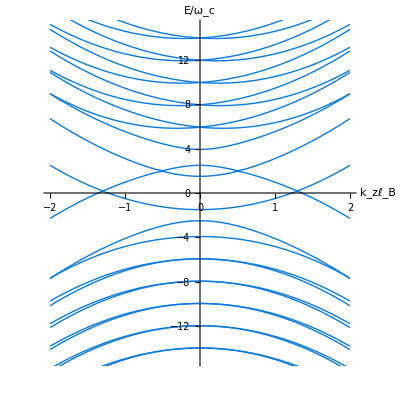

BLL.pdf

```mathematica
LMX=DiscretePlot[Sort[Re[Eigenvalues[3 LandMat[40,1,1,kz]]]],{kz,-2,2,0.1},AspectRatio->1,Joined->True,Filling->None,PlotRange->{-15,15},PlotStyle->Directive[RGBColor[12/255,123/255,220/255],Thick],TicksStyle-> Directive[FontSize-> 25,FontFamily -> "Latin Modern Roman",FontColor->Black],AxesStyle->Directive[Black,Thickness[0.005]],AxesLabel->{Style["k_zℓ_B",FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontSize->40,FontColor->Black],Style["E/ω_c",FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontSize->40,FontColor->Black]}]
Export["BLL.pdf",LMX]
```